Your Title Here

```mathematica
Manipulate[
Module[{type,colL,colV,δx,δy,δw,δh,th1,th2,vaporize,condense,p1,p2,p3},
type=Which[q<0,Column[{"superheated","vapor"},Center],q==0,Column[{"dew-point","vapor"},Center],0<q<1,Column[{"partially","vaporized"},Center],q==1,Column[{"bubble-point","liquid"},Center],q>1,Column[{"subcooled","liquid"},Center]];

colL=Blue;colV=RGBColor[0,0.7,0];
δx=1;δy=0.4*δx;δw=0.35*δx;δh=0.5*δy;
th1=0.015;th2=0.007;

vaporize=Module[{f1,f2,col},
f1=Quiet@Interpolation[BezierFunction[{{0.25*δx,δy},{0.5*δx,0.5*δy},{0.65*δx,δy+δh}}][#]&/@Range[0,δx,0.05]];
f2={#,f1[#]}&/@Range[0.25*δx,0.65*δx,0.01];
col[x_]:=Blend[{colL,colV},Rescale[x,{1,Length@f2-1}]];
{Thickness@th2,{col[#],Line[{f2[[#]],f2[[#+1]]}]}&/@Range[1,Length@f2-2],
colV,Arrow[{f2[[-2]],f2[[Length@f2]]}]
}];

condense=Module[{f1,f2,col},
f1=Quiet@Interpolation[BezierFunction[{{0.75*δx,δy},{0.3*δx,δy},{0.3*δx,-δh}}][#]&/@Range[0,1,0.05]];
f2=Reverse[{#,f1[#]}&/@Range[0.3*δx,0.75*δx,0.01]];
col[x_]:=Blend[{colV,colL},Rescale[x,{25,Length@f2}]];
{Thickness@th2,{col[#],Line[{f2[[#]],f2[[#+1]]}]}&/@Range[1,Length@f2-2],
colL,Arrow[{f2[[-2]],f2[[Length@f2]]}]}];

p1=Graphics[{
{EdgeForm@Thick,FaceForm@GrayLevel@0.95,Rectangle[{0,0},{δx,δy}]},
Thick,Line[{{#,-0.5*δy},{#,1.5*δy}}]&/@{0,δx},
Arrowheads@0.06,Which[
q<0,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L"}," < "],25],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V","F"},{" > "," + "}],25],{0.75*δx,δy+δh},{0,-1.5}],
vaporize,colV,Thickness@th1,Arrow@BezierCurve[{{0,δy/2},{0.7*δx,δy/2},{0.7*δx,δy+δh}}]},
q==0,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L"}," = "],25],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V","F"},{" = "," + "}],25],{0.75*δx,δy+δh},{0,-1.5}],
colV,Thickness@th1,Arrow@BezierCurve[{{0,δy/2},{0.7*δx,δy/2},{0.7*δx,δy+δh}}]},
0<q<1,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L",Subscript["L",Style["F",FontSlant->Plain]]},{" = "," + "}],25],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V",Subscript["V",Style["F",FontSlant->Plain]]},{" = "," + "}],25],{0.75*δx,δy+δh},{0,-1.5}],
colL,Thickness[q*th1],Arrow@BezierCurve[{{0,δy/2},{0.2*δx,δy/2},{0.2*δx,-δh}}],
colV,Thickness[(1-q)*th1],Arrow@BezierCurve[{{0,δy/2},{0.7,δy/2},{0.7,δy+δh}}]},
q==1,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L","F"},{" = "," + "}],25],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V"}," = "],25],{0.75*δx,δy+δh},{0,-1.5}],
colL,Thickness@th1,Arrow@BezierCurve[{{0,δy/2},{0.2*δx,δy/2},{0.2*δx,-δh}}]},
q>1,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L","F"},{" > "," + "}],25],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V"}," < "],25],{0.75*δx,δy+δh},{0,-1.5}],
condense,colL,Thickness@th1,Arrow@BezierCurve[{{0,δy/2},{0.2*δx,δy/2},{0.2*δx,-δh}}]}]
}];

p2=Graphics[{
{Thickness@th2,Arrowheads@0.06,
Arrow[{{-δw,δy/2},{0,δy/2}}],
colL,Arrow[{{0.25*δx,δy+δh},{0.25*δx,δy}}],Arrow[{{0.25*δx,0},{0.25*δx,-δh}}],
colV,Arrow[{{0.75*δx,δy},{0.75*δx,δy+δh}}],
Arrow[{{0.75*δx,-δh},{0.75*δx,0}}]},
Text[Style["L",25,Italic],{0.25*δx,δy+δh},{0,-1.5}],
Text[Style[OverBar@Style["V",Italic],25],{0.75*δx,-δh},{0,1.5}],
Text[Style[Column[{Row@{"feed ",Style["F",Italic]},type},Center,Spacings->1.5],22],{-δw/2,δy/2},{0,0.37}]
}];

Show[p1,p2,ImageSize->{600,400},AspectRatio->Full,PlotRange->{{-δw,δx},{-δh,δy+δh}},PlotRangePadding->{{None,0.01},Scaled@0.1}]
],
Control[{{q,-0.5,"feed quality"},-0.5,1.5,0.1,Appearance->"Labeled"}]
]
```

```mathematica
(*,
Control[{{min,1},-5,25,1,Appearance->"Labeled"}],
Control[{{max,10},5,15,1,Appearance->"Labeled"}]*)
```

```mathematica
(*{#,Blend[{colV,colL},Rescale[#,{min,max}]]}&/@Range[min,max,1]*)
(*Module[{f1,f2,col},
f1=Quiet@Interpolation[BezierFunction[{{0.75*δx,δy},{0.3*δx,δy},{0.3*δx,-δh}}][#]&/@Range[0,1,0.05]];
f2=Reverse[{#,f1[#]}&/@Range[0.3*δx,0.75*δx,0.01]];
Length@f2]*)
```

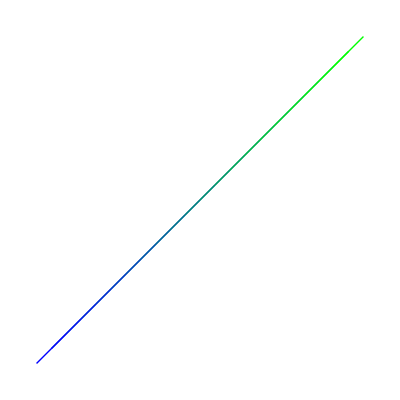

```mathematica
Graphics[{Thick,Blend[{Blue,Green},#],Line[{{#,#},{#+0.1,#+0.1}}]}&/@Range[0,1,0.05]]
```

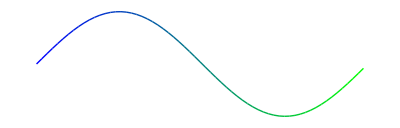

```mathematica
Module[{data},
data={#,Sin[#]}&/@Range[0,2*π,0.1];
Graphics[{Thick,Blend[{Blue,Green},Rescale[#,{1,Length@data-1}]],Line[{data[[#]],data[[#+1]]}]}&/@Range[1,Length@data-1]]
]
```

```mathematica
Module[{f1,col,f2},
f1=Quiet@Interpolation[BezierFunction[{{0.25*δx,δy},{0.5*δx,0.5*δy},{0.65*δx,δy+δh}}][#]&/@Range[0,δx,0.05]];
col[x_]:=Blend[{Blue,Green},Rescale[f1[x],{0.5*δy,δy+δh}]];
Plot[f1[x],{x,0.25*δx,0.65*δx},PlotStyle->Thickness@th2,ColorFunction->(col[#1]&),ColorFunctionScaling->False];

f2={#,f1[#]}&/@Range[0.25*δx,0.65*δx,0.01];
Graphics[{Thickness@th2,Arrow@Line[f2,VertexColors->Join[ConstantArray[colL,Round[0.5*Length@f2]],ConstantArray[colV,Round[0.5*Length@f2]]]]}];

Graphics[{Thickness@th2,colV,Arrow@Line[f2,VertexColors->(Blend[{colL,colV},Rescale[#,{0.25*δx,0.65*δx}]]&/@Range[0.25*δx,0.65*δx,0.01])]}]
]
```

```mathematica
(0.25+0.65)/2
```

0.45

```mathematica
p1=Graphics[{Arrowheads@0.06,
{EdgeForm@Thick,FaceForm@GrayLevel@0.95,Rectangle[{0,0},{δx,δy}]},
Thick,Which[
q<0,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L"}," < "],20],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V","F"},{" > "," + "}],20],{0.75*δx,δy+δh},{0,-1.5}],
colL,Thickness[-q*th1],Arrow@BezierCurve[{{0.25*δx,δy},{0.5*δx,0.5*δy},{0.65*δx,δy+δh}}],
colV,Thickness@th1,Arrow@BezierCurve[{{0,δy/2},{0.7*δx,δy/2},{0.7*δx,δy+δh}}]},
q==0,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L"}," = "],20],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V","F"},{" = "," + "}],20],{0.75*δx,δy+δh},{0,-1.5}],
colV,Thickness@th1,Arrow@BezierCurve[{{0,δy/2},{0.7*δx,δy/2},{0.7*δx,δy+δh}}]},
0<q<1,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L",Subscript["L",Style["F",FontSlant->Plain]]},{" = "," + "}],20],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V",Subscript["V",Style["F",FontSlant->Plain]]},{" = "," + "}],20],{0.75*δx,δy+δh},{0,-1.5}],
colL,Thickness[q*th1],Arrow@BezierCurve[{{0,δy/2},{0.2*δx,δy/2},{0.2*δx,-δh}}],
colV,Thickness[(1-q)*th1],Arrow@BezierCurve[{{0,δy/2},{0.7,δy/2},{0.7,δy+δh}}]},
q==1,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L","F"},{" = "," + "}],20],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V"}," = "],20],{0.75*δx,δy+δh},{0,-1.5}],
colL,Thickness@th1,Arrow@BezierCurve[{{0,δy/2},{0.2*δx,δy/2},{0.2*δx,-δh}}]},
q>1,{
Text[Style[Row@Riffle[Style[#,Italic]&/@{OverBar@"L","L","F"},{" > "," + "}],20],{0.25*δx,-δh},{0,1.5}],
Text[Style[Row@Riffle[Style[#,Italic]&/@{"V",OverBar@"V"}," < "],20],{0.75*δx,δy+δh},{0,-1.5}],
colV,Thickness[(q-1)*th1],Arrow@BezierCurve[{{0.75*δx,δy},{0.3*δx,δy},{0.3*δx,-δh}}],
colL,Thickness@th1,Arrow@BezierCurve[{{0,δy/2},{0.2*δx,δy/2},{0.2*δx,-δh}}]}]
}];
```





```mathematica
p2=Graphics[{
{Thickness@th2,Arrowheads@0.06,
Arrow[{{-δw,δy/2},{0,δy/2}}],
colL,
{Thickness@If[q<0,(1+q)*th2,th2],Arrow[{{0.25*δx,δy+δh},{0.25*δx,δy}}]},
{Thickness@Which[q≤0,th2,0<q≤1,th2+q*th1,q>1,th2+th1+(q-1)*th1],Arrow[{{0.25*δx,0},{0.25*δx,-δh}}]},
colV,
{Thickness@Which[q<0,th2+(1-q)*th1,q==0,th1+th2,0<q<1,(1-q)*th1+th2,q==1,th2,q>1,(1-(q-1))*th2],Arrow[{{0.75*δx,δy},{0.75*δx,δy+δh}}]},
Arrow[{{0.75*δx,-δh},{0.75*δx,0}}]},
Text[Style["L",20,Italic],{0.25*δx,δy+δh},{0,-1.5}],
Text[Style[OverBar@Style["V",Italic],20],{0.75*δx,-δh},{0,1.5}],
Text[Style[Column[{Row@{"feed ",Style["F",Italic]},type},Center,Spacings->2],18],{-δw/2,δy/2},{0,0.15}]
}];
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX